29

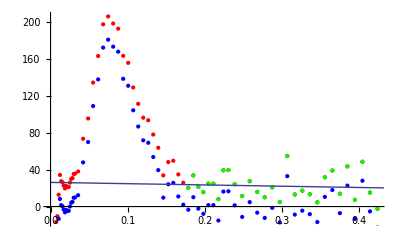

{26.2496-13.8354 x, | Estimate | Standard Error | t-Statistic | P-Value
a | -13.8354 | 35.6281 | -0.388328 | 0.700818
b | 26.2496 | 10.7408 | 2.44392 | 0.0213441}

```mathematica
prefix = "PET-";
sample = "215";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".0.phg","Table"];

data = Take[rawData, -(Length[rawData]-7)];

toRel[array_] := {array[[1]]/(2*Pi) * 10, array[[2]]*(array[[1]] /(2*Pi))^2 * 100};
rel = Map[toRel, data];

sampleSize = 29
notSample = Length[data ] - sampleSize;

linearData =  Take[rel, -sampleSize];
nonLinearData = Take[rel, Length[data ] - sampleSize];
lFit = NonlinearModelFit[linearData,a x + b,{a,b},{x}];

correct[a_] := {a[[1]], a[[2]]-lFit["Function"][a[[1]]]}
correctedRel = Map[correct, rel];


Show[ListPlot[rel,PlotStyle->Red], ListPlot[correctedRel,PlotStyle->Blue], ListPlot[linearData,PlotStyle->Green],Plot[{lFit["BestFit"]},{x,0,0.44}]]

lFit[{"BestFit","ParameterTable"}]

switch[a_] := {a[[2]], a[[1]]}
correctedRelOutput = Map[switch, correctedRel];

Export[path<>".rel", correctedRel, "Table"];
Export[path <> ".fit", lFit["BestFit"], "String"];
Export[path<>"-fitPoints.rel", linearData, "Table"];
Export[path<>"-nonFitPoints.rel", nonLinearData, "Table"];
```